Vojtěch Myslivec, FIT ČVUT v Praze, 2015/2016

# Kryptosystém McEliece

Ukázka použití kryptosystému McEliece pro asymetrické šifrování.

## Pomocné funkce

### nahodnaPermutacniMatice

Náhodná permutační matice n×n

```mathematica
Unprotect[nahodnaPermutacniMatice];
ClearAll[nahodnaPermutacniMatice];

nahodnaPermutacniMatice[n_]:=RandomSample[IdentityMatrix[n]]

Protect[nahodnaPermutacniMatice];
```

### nahodnaRegularniMatice

Náhodná regulární matice k×k (nad ℤ_2)

```mathematica
Unprotect[nahodnaRegularniMatice];
ClearAll[nahodnaRegularniMatice];

nahodnaRegularniMatice[k_]:=Module[
{r=0,M,i=0},
While[
r≠k,
M=RandomChoice[{0,1},{k,k}];
r=MatrixRank[M,Modulus->2];
i++
];
(*{M,i}*)
M
]

Protect[nahodnaRegularniMatice];
```

## Generování klíčů

Lineární kód (n,k) opravující t chyb,
 - generujici matice G
 - náhodná k×k regulární matice S
 - náhodná n×n permutační matice P

```mathematica
p=2;
m=4;
t=3;
n=p^m;
k=n-m t;
GoppaKod=generujBinarniGoppaKod[m,t];
G=GoppaKod⟦1⟧;
S=nahodnaRegularniMatice[k];
P=nahodnaPermutacniMatice[n];
hatG=dotNad2[S,G,P];
```

```mathematica
mG=G//MatrixForm;
mS=S//MatrixForm;
mP=P//MatrixForm;
mhatG=hatG//MatrixForm;
(*
Print["G = ",mG];
Print["S = ",mS];
Print["P = ",mP];
*)
Print["Ĝ = SGP = ",mS,mG,mP ,"=",mhatG];
```

Ĝ = SGP = (0 | 1 | 1 | 0
1 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 1 | 0 | 1)(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0)(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)=(1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1)

Parametry (n, k, t), veřejný klíč (OverHat[G)], soukromý klíč (G, S^-1, P^-1)

```mathematica
parametry={n,k,t};
verejnyKlic={hatG};
soukromyKlic={GoppaKod,Inverse[S,Modulus->2],Inverse[P,Modulus->2]};
```

```mathematica
ClearAll[n,k,t,hatG,G,GoppaKod,S,P,invS,invP]
```

## Šifrování

Algoritmus: “zakódovat” zprávu m (délky k), pomocí “generující” matice Ĝ a přičíst náhodný chybový vektor z (délky n) s Hammingovou vahou max. t
c=m Ĝ+z

```mathematica
n=parametry⟦1⟧;
k=parametry⟦2⟧;
t=parametry⟦3⟧;
hatG=verejnyKlic⟦1⟧;

zprava=m=nahodnyPolynom[p,k];
If[Length[m]≠k,Print["Chyba, zpráva m musí být délky k"]];
z=nahodnyChybovyVektor[n,t-1]
c=plus[dotNad2[m,hatG],z,p]
```

{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1}

{0,1,0,1,0,0,0,0,1,0,0,1,0,1,1,1}

```mathematica
ClearAll[n,k,t,hatG,G,S,P,invS,invP,m]
```

## Dešifrování

Algoritmus:
 - získat ĉ=c P^-1 -- inverze permutace
 - dekódovat m̂ z ĉ -- kód odstraní chybový vektor
 - vypočítat původní zprávu m=m̂ S^-1

```mathematica
GoppaKod=soukromyKlic⟦1⟧;
invS=soukromyKlic⟦2⟧;
invP=soukromyKlic⟦3⟧;

hatc=dotNad2[c,invP];
hatm=dekodujBinarniGoppaKod[hatc,GoppaKod]⟦1⟧;
m=dotNad2[hatm,invS]
m==zprava
```

{1,0,1,0}

True

```mathematica
ClearAll[n,k,t,hatG,G,S,P,invS,invP,m,hatc,hatm]
```

## Časové složitosti

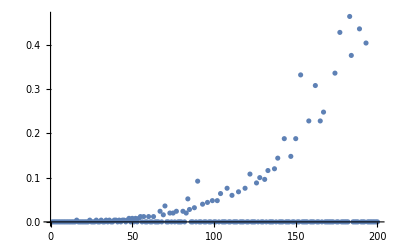

```mathematica
cas={#,Timing[nahodnaRegularniMatice[#]]⟦1⟧}&/@Range[200];
ListPlot[cas,PlotRange->All]
```